#### Problem description

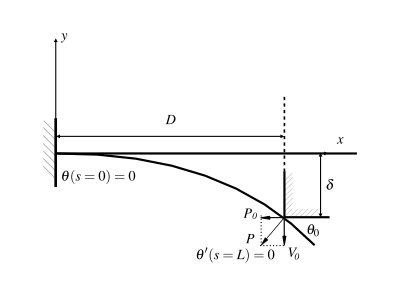

The governing equation for the Euler Elastica problem is

E I (d^2 θ)/(d s^2)-P_0 sin(θ)+ V_0 cos(θ)=0

where 0≤s≤L is the arc length coordinate, θ is the angle of deflection (in radians) at point s, P_0 (positive when pointing to right) and V_0(positive when pointing upward) are the horizontal and vertical forces at the right end of the beam, respectively.

Let ξ=s/L, then the equation becomes

(E I)/L^2 (d^2 θ)/dξ^2-P_0 sin(θ)+ V_0 cos(θ)=0

Note that

-P_0=P sin(-θ_0)-μ P cos(θ_0)
-V_0=P cos(θ_0)+μ P sin(-θ_0)

P_0=P sin(θ_0)+μ P cos(θ_0)=P( sin(θ_0)+μ cos(θ_0))
V_0=-P cos(θ_0)+μ P sin(θ_0)=-P(cos(θ_0)-μ sin(θ_0))

where θ_0=θ(ξ=1)<0, P>0 is the magnitude of the reaction force. Thus

(E I)/(P L^2) (d^2 θ)/(d ξ^2)-( sin(θ_0)+μ cos(θ_0))sin(θ)- (cos(θ_0)-μ sin(θ_0))cos(θ)=0
 (d^2 θ)/dξ^2-(P L^2)/(E I) (cos(θ_0-θ)-μ sin(θ_0-θ))=0

Let k=(P L^2)/(E I), f=θ-θ_0. Note that

f(ξ=0)=θ(ξ=0)-θ_0=-θ_0
f(ξ=1)=θ(ξ=1)-θ_0=0
f'(ξ=1)=θ'(ξ=1)=0

The simplified governing equation and boundary conditions are as follows

(d^2 f)/dξ^2-k (cos(f)-μ sin(f))=0
f(1)=0
f'(1)=0
f(0)=-θ_0

And we also have

D=L∫_0^1 cos(θ(ξ)) dξ=L∫_0^1 cos(f-f(0)) dξ
δ=L∫_0^1 sin(θ(ξ)) dξ=L∫_0^1 sin(f-f(0)) dξ
(P D^2)/(E I)=k (D/L)^2=(k(∫_0^1 cos(f-f(0)) dξ))^2
δ/D=(∫_0^1 sin(f-f(0)) dξ)/(∫_0^1 cos(f-f(0)) dξ)

### Moment-deflection relations

k=(P L^2)/(E I)
V_0=-P (cos(θ_0)-μ sin(θ_0))
F=-2 V_0=2P(cos(θ_0)-μ sin(θ_0))
(F D^2)/(E I)=(P L^2)/(E I)2(cos(θ_0)-μ sin(θ_0))
(F D^2)/(E I)=2k (cos(θ_0)-μ sin(θ_0))
M=δ P_0-D V_0
...

```mathematica
μ=0.93;
```

```mathematica
δPCurve=ParallelTable[solf=NDSolve[{f''[ξ]-k( Cos[f[ξ]]-μ Sin[f[ξ]])==0,f[1]==0,f'[1]==0},f,{ξ,0,1}];DL=NIntegrate[Cos[(f[ξ]-f[0])/.solf[[1]]],{ξ,0,1}];
δL=NIntegrate[Sin[(f[ξ]-f[0])/.solf[[1]]],{ξ,0,1}];
{2k*DL^2 Cos[f[0]/.solf[[1]]],-δL/DL,k,f[0]/.solf[[1]],k(δL/DL Sin[f[0]/.solf[[1]]]+Cos[f[0]/.solf[[1]]]),-D[f[ξ]/.solf[[1]],ξ]/.ξ->0},{k,0.02,3,0.02}];
```

ParallelTable::nopar: No parallel kernels available; proceeding with sequential evaluation.

```mathematica
Isp=δPCurve[[Position[δPCurve[[;;,1]],Max[δPCurve[[;;,1]]]][[1]]]][[1]]
```

{1.91615,0.508755,1.7,0.729129,0.691581,1.20881}

```mathematica
SetDirectory[NotebookDirectory[]];
Save["dpCurveWithFriction",δPCurve]
```

```mathematica
SetDirectory[NotebookDirectory[]];
(*Get["dpCurveWithFriction"];*)
Isp=δPCurve[[Position[δPCurve[[;;,1]],Max[δPCurve[[;;,1]]]][[1]]]][[1]]
```

Get::noopen: Cannot open dpCurve.

{1.66795,0.477411,1.36,0.669755,0.663136,1.29945}

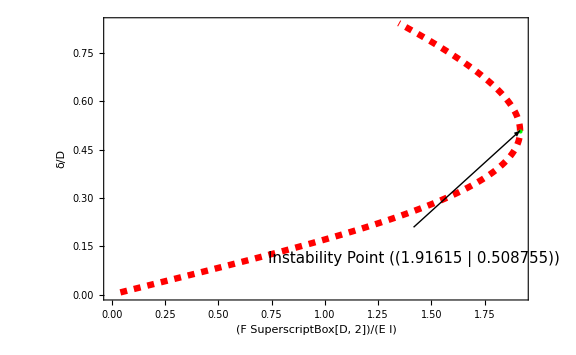

```mathematica
ListPlot[δPCurve[[;;,1;;2]],Joined->False];
pIsp=Graphics[{PointSize[Large],Green,Point[Isp[[1;;2]]]}];
pArrow=Graphics[Arrow[{Isp[[1;;2]]+{-0.5,-0.3},Isp[[1;;2]]}]];
ptext=Graphics[Text[Style["Instability Point "@{Isp[[1;;2]]},FontSize->15],Isp[[1;;2]]+{-0.5,-0.4}]];
p1=ListPlot[δPCurve[[;;,1;;2]],Joined->True,PlotStyle->Directive[Red,Thickness[0.008],Dashed],PlotRange->Automatic,ImageSize->Large,GridLines->None,Ticks->Automatic,AxesStyle->Directive[Black,FontFamily->"Times",16],Frame->True,FrameStyle->Directive[FontFamily->"Times",12],FrameLabel->{Style["(F SuperscriptBox[D, 2])/(E I)",Black,FontFamily->"Times",16],Style["δ/D",Black,FontFamily->"Times",16]}];
Show[p1,pIsp,pArrow,ptext]
```

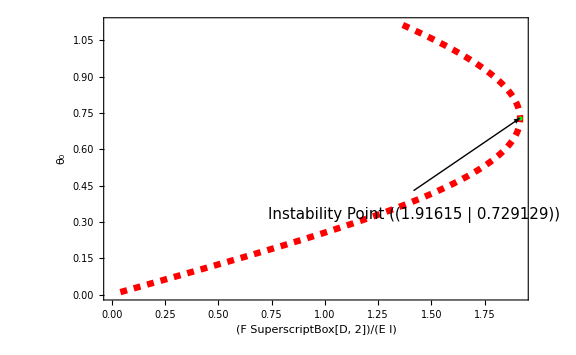

```mathematica
pIsp=Graphics[{PointSize[Large],Green,Point[Isp[[1;;4;;3]]]}];
pArrow=Graphics[Arrow[{Isp[[1;;4;;3]]+{-0.5,-0.3},Isp[[1;;4;;3]]}]];
ptext=Graphics[Text[Style["Instability Point "@{Isp[[1;;4;;3]]},FontSize->15],Isp[[1;;4;;3]]+{-0.5,-0.4}]];
p2=ListPlot[δPCurve[[;;,1;;4;;3]],Joined->True,PlotStyle->Directive[Red,Thickness[0.008],Dashed],PlotRange->Automatic,ImageSize->Large,GridLines->None,Ticks->Automatic,AxesStyle->Directive[Black,FontFamily->"Times",16],Frame->True,FrameStyle->Directive[FontFamily->"Times",12],FrameLabel->{Style["(F SuperscriptBox[D, 2])/(E I)",Black,FontFamily->"Times",16],Style["θ_0",Black,FontFamily->"Times",16]},
RotateLabel->False];
Show[p2,pIsp,pArrow,ptext]
```

### Deflection-k

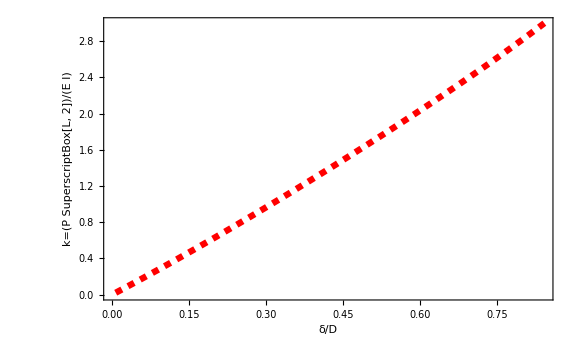

```mathematica
p3=ListPlot[δPCurve[[;;,{2,3}]],Joined->True,PlotStyle->Directive[Red,Thickness[0.008],Dashed],PlotRange->Automatic,ImageSize->Large,GridLines->None,Ticks->Automatic,AxesStyle->Directive[Black,FontFamily->"Times",16],Frame->True,FrameStyle->Directive[FontFamily->"Times",12],FrameLabel->{Style["δ/D",Black,FontFamily->"Times",16],Style["k=(P SuperscriptBox[L, 2])/(E I)",Black,FontFamily->"Times",16]},RotateLabel->False]
```

### Load-k

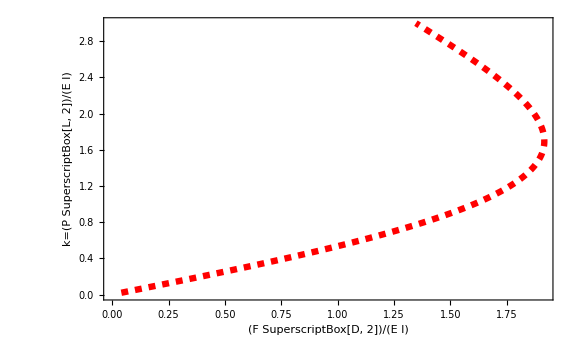

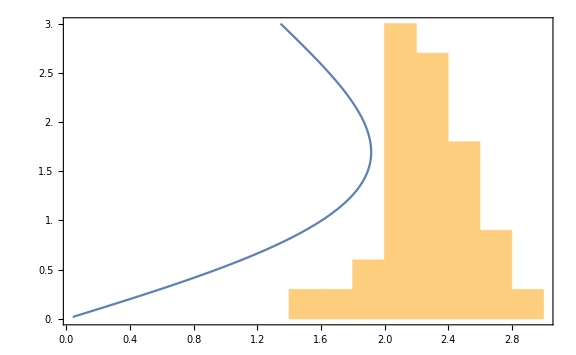

```mathematica
p3=ListPlot[δPCurve[[;;,{1,3}]],Joined->True,PlotStyle->Directive[Red,Thickness[0.008],Dashed],PlotRange->Automatic,ImageSize->Large,GridLines->None,Ticks->Automatic,AxesStyle->Directive[Black,FontFamily->"Times",16],Frame->True,FrameStyle->Directive[FontFamily->"Times",12],FrameLabel->{Style["(F SuperscriptBox[D, 2])/(E I)",Black,FontFamily->"Times",16],Style["k=(P SuperscriptBox[L, 2])/(E I)",Black,FontFamily->"Times",16]},RotateLabel->False]
Module[{fgraph,ggraph,frange,grange,fticks,gticks},
{fgraph,ggraph}={ListPlot[δPCurve[[;;,{1,3}]],Joined->True],Histogram[FexpAll]};
frange=(PlotRange/.AbsoluteOptions[fgraph,PlotRange])[[2]];
grange={0,10};
fticks=N@FindDivisions[frange,6];
gticks=Quiet@Transpose@{fticks,ToString[NumberForm[#,2],StandardForm]&/@Rescale[fticks,frange,grange]};
Show[fgraph,ggraph/.Graphics[graph_,s___]:>Graphics[GeometricTransformation[graph,RescalingTransform[{{0,1},grange},{{0,1},frange}]],s],Axes->False,Frame->True,FrameStyle->{ColorData[1]/@{1,2},{Automatic,Automatic}},FrameTicks->{{fticks,gticks},{Automatic,Automatic}},
PlotRange->All]
]
```

### Curvature-k

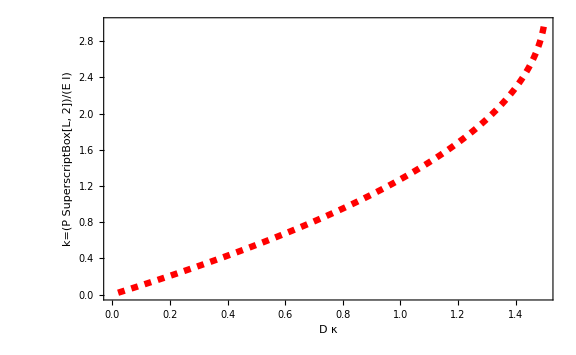

```mathematica
p3=ListPlot[δPCurve[[;;,{6,3}]],Joined->True,PlotStyle->Directive[Red,Thickness[0.008],Dashed],PlotRange->Automatic,ImageSize->Large,GridLines->None,Ticks->Automatic,AxesStyle->Directive[Black,FontFamily->"Times",16],Frame->True,FrameStyle->Directive[FontFamily->"Times",12],FrameLabel->{Style["D κ",Black,FontFamily->"Times",16],Style["k=(P SuperscriptBox[L, 2])/(E I)",Black,FontFamily->"Times",16]},RotateLabel->False]
```

```mathematica
Position[δPCurve[[;;,1]],Max[δPCurve[[;;,1]]]][[1]]
Isp
```

{85}

{1.91615,0.508755,1.7,0.729129,0.691581,1.20881}

```mathematica
Length@δPCurve
```

150

```mathematica
gd[x_]=Fit[δPCurve[[1;;100,{2,3}]],{1,x,x^2,x^3},x]
gp[x_]=Fit[δPCurve[[1;;85,{1,3}]],{1,Sin[x],Sin[2x],Sin[3 x],Sin[4x],Sin[5 x],Sin[6 x],Sin[7 x]},x]
gk[x_]=Fit[δPCurve[[1;;85,{6,3}]],{1,Sin[x],Sin[2x],Sin[3 x],Sin[4x]},x]
```

-0.000720766+3.0207 x+0.708182 x^2-0.144685 x^3

-0.0171387+3.69939 Sin[x]-4.55259 Sin[2 x]+4.2579 Sin[3 x]-3.07682 Sin[4 x]+1.71326 Sin[5 x]-0.682778 Sin[6 x]+0.162496 Sin[7 x]

-0.0012575+3.58795 Sin[x]-2.16728 Sin[2 x]+0.793296 Sin[3 x]-0.151186 Sin[4 x]

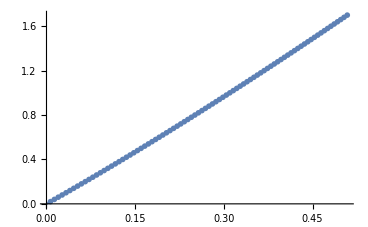

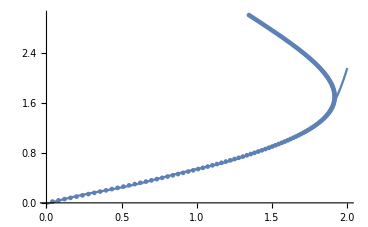

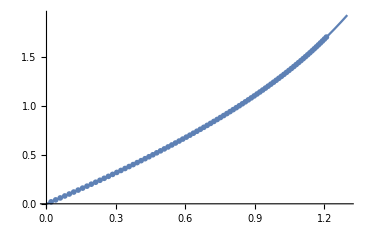

```mathematica
Show[Plot[gd[x],{x,0,0.477410963901491}],ListPlot[δPCurve[[1;;85,{2,3}]]],PlotRange->All]
Show[Plot[gp[x],{x,0,2}],ListPlot[δPCurve[[;;,{1,3}]]],PlotRange->All]
Show[Plot[gk[x],{x,0,1.299}],ListPlot[δPCurve[[1;;85,{6,3}]]],PlotRange->All]
```

Euler-Bernoulli beam

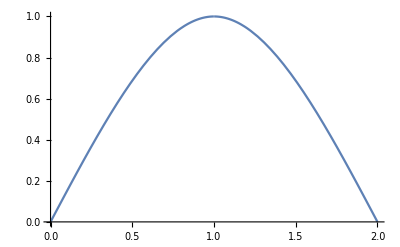

```mathematica
(*y[x_,δ_,]*)
y[δ_,x_]=δ Piecewise[{{x/2(3-4(x/2)^2),0<x≤1},{(2-x)/2(3-4((2-x)/2)^2),1<x≤2}}];
Plot[y[1,x],{x,0,2}]
```

Compare with experimental shape of EA

```mathematica
CompareEA[fn_]:=Module[{fname = fn,nn},
SetDirectory[NotebookDirectory[]];
Get[fname];
zw=Partition[Riffle[z,w],2];
pe=ListPlot[zw/DD];
nn=If[(F DD^2)/EI>1.9161518201003527,{1},{1,3}];
(*nn=1;*)
klist = {gd[dflec/DD],gk[DD kappa],gp[(F DD^2)/EI]};
textlist= {"Same deflection: ","Same curvature : ","Same load      : "};
Colorlist = {Red,Yellow,Purple};
Print["Test ID: ", fn];
Print["{F,δ,k,θ_0,M,κ} : ",Blue,{(F DD^2)/EI,dflec/DD,k,Theta,(F DD)/(2 EI)(DD+dflec*Tan[Theta]),DD kappa}];
pt=Module[{k=klist[[#]]},
solf=NDSolve[{f''[ξ]-k( Cos[f[ξ]]-μ Sin[f[ξ]])==0,f[1]==0,f'[1]==0},f,{ξ,0,1}];
DL=NIntegrate[Cos[(f[ξ]-f[0])/.solf[[1]]],{ξ,0,1}];
δL=NIntegrate[Sin[(f[ξ]-f[0])/.solf[[1]]],{ξ,0,1}];
solx = NDSolve[{x'[s]==-Cos[f[s]-f[0]/.solf[[1]]],x[1]==0},x[s],{s,0,1}];
soly = NDSolve[{y'[s]==Sin[f[s]-f[0]/.solf[[1]]],y[1]==0},y[s],{s,0,1}];
Print[textlist[[#]],Colorlist[[#]],{2k*DL^2 Cos[f[0]/.solf[[1]]],-δL/DL,k,f[0]/.solf[[1]],k(δL/DL Sin[f[0]/.solf[[1]]]+Cos[f[0]/.solf[[1]]]),-D[f[ξ]/.solf[[1]],ξ]/.ξ->0}];
ParametricPlot[{{x[s]/DL/.solx[[1]],y[s]/DL/.soly[[1]]},{2-x[s]/DL/.solx[[1]],y[s]/DL/.soly[[1]]}},{s,0,1},
PlotStyle->Directive[Colorlist[[#]],Thickness[0.004],Dashed],
(*PlotLegends->Placed[{k},{0.5,0.5}],*)
ImageSize->Large,GridLines->None,Ticks->Automatic,AxesStyle->Directive[Black,FontFamily->"Times",16],Frame->True,FrameStyle->Directive[FontFamily->"Times",12],FrameLabel->{Style["x/D",Black,FontFamily->"Times",16],Style["w/D",Black,FontFamily->"Times",16]}]]&/@nn;
AppendTo[pt,pe];
peb=Plot[y[dflec/DD,x],{x,0,2},PlotStyle->Directive[Green,Thickness[0.004],Dashed]];
Show[Append[pt,peb],PlotRange->All]]
```

```mathematica
Isp={1.9161518201003527,0.508754730010644,1.7,0.7291291044265703,0.6915805820664326,1.2088119094315215}
```

{1.91615,0.508755,1.7,0.729129,0.691581,1.20881}

δPCurve = {(F D^2)/(E I),-δ/D,(P L^2)/(E I)=k,-θ_0,-(M D)/(E I),D κ}
δPCurve = {F,δ,k,θ_0,M, κ}

{1.63204,0.353101,1.14782,0.55094,0.993052,0.858285}

{True,True,True,True,False,True}

Test ID: EA_5

{F,δ,k,θ_0,M,κ} : RGBColor[0, 0, 1]{1.63204,0.353101,k,0.55094,0.993052,0.858285}

Same deflection: RGBColor[1, 0, 0]{1.72839,0.353039,1.14782,0.519595,0.795123,0.926326}

Same load      : RGBColor[0.5, 0, 0.5]{1.63249,0.318891,1.03015,0.471509,0.768524,0.852511}

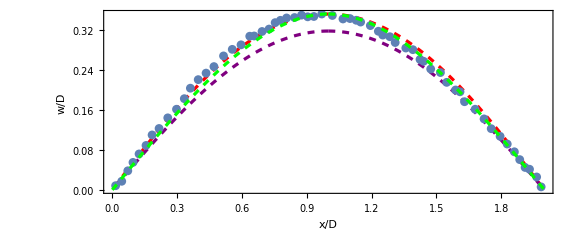

```mathematica
SetDirectory[NotebookDirectory[]];
fn="EA_5";
Get[fn];
ExperData={(F DD^2)/EI,dflec/DD,gd[dflec/DD],Theta,(F DD)/(2 EI)(DD+dflec*Tan[Theta]),DD kappa}
Isp[[#]]>ExperData[[#]]&/@Range[Length@Isp]
CompareEA[fn]
```

δPCurve = {(F D^2)/(E I),-δ/D,(P L^2)/(E I)=k,-θ_0,-(M D)/(E I),D κ}
δPCurve = {F,δ,k,θ_0,M, κ}

```mathematica
Get["EAinx"]
```

{3,5,6,8,9,11,12,13,14,16,17,18,19,21,22,23,26,27,29,30,31,33,34,35,36,37,38,39,40,41,42,43,44}

```mathematica
ClearAll[epsilon]
```

```mathematica
Fexp[fn_]:=Module[{fname = fn},
Get[fname];
(F DD^2)/EI]
ϵexp[fn_]:=Module[{fname = fn},
Get[fname];
epsilon]
KappaElastica[fn_]:=Module[{fname = fn,k},
Get[fname];
k=gd[dflec/DD];
solf=NDSolve[{f''[ξ]-k Cos[f[ξ]]==0,f[1]==0,f'[1]==0},f,{ξ,0,1}];
(-D[f[ξ]/.solf[[1]],ξ]/.ξ->0)/DD
]
```

```mathematica
fn="EA_"<>ToString[#]&/@EAinx;
FexpAll=Table[Fexp[fn[[n]]],{n,1,Length@EAinx}];
ϵexpAll=Table[ϵexp[fn[[n]]],{n,1,Length@EAinx}];
κAll=Table[KappaElastica[fn[[n]]],{n,1,Length@EAinx}]
```

{2670.05,1877.14,2186.17,2798.8,2812.23,1981.76,2801.73,2229.25,2386.36,1810.16,2389.93,2985.86,1885.79,3118.89,2259.49,3437.26,2560.51,3640.35,3530.32,3562.66,2942.48,2738.98,2114.94,2745.1,3646.41,2286.77,2254.68,2265.54,2654.02,3072.78,2090.81,2473.22,3161.35}

## The experimental forces are typically larger than the instability forces because of the existence of the friction

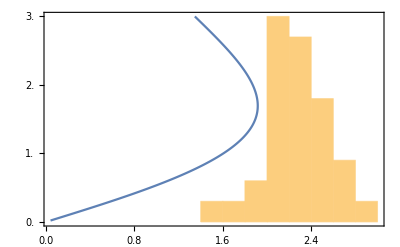

```mathematica
Module[{fgraph,ggraph,frange,grange,fticks,gticks},
{fgraph,ggraph}={ListPlot[δPCurve[[;;,{1,3}]],Joined->True],Histogram[FexpAll]};
frange=(PlotRange/.AbsoluteOptions[fgraph,PlotRange])[[2]];
grange={0,10};
fticks=N@FindDivisions[frange,6];
gticks=Quiet@Transpose@{fticks,ToString[NumberForm[#,2],StandardForm]&/@Rescale[fticks,frange,grange]};
Show[fgraph,ggraph/.Graphics[graph_,s___]:>Graphics[GeometricTransformation[graph,RescalingTransform[{{0,1},grange},{{0,1},frange}]],s],Axes->False,Frame->True,FrameStyle->{ColorData[1]/@{1,2},{Automatic,Automatic}},FrameTicks->{{fticks,gticks},{Automatic,Automatic}},
PlotRange->All]
]
```

## Offset of the loading point

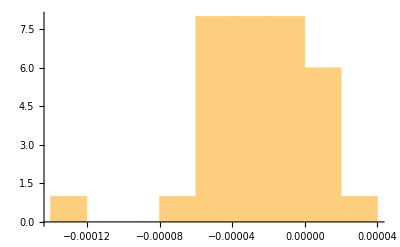

```mathematica
Histogram[ϵexpAll]
```

{EA_3,EA_5,EA_6,EA_8,EA_9,EA_11,EA_12,EA_13,EA_14,EA_16,EA_17,EA_18,EA_19,EA_21,EA_22,EA_23,EA_26,EA_27,EA_29,EA_30,EA_31,EA_33,EA_34,EA_35,EA_36,EA_37,EA_38,EA_39,EA_40,EA_41,EA_42,EA_43,EA_44}

Test ID: EA_3

{F,δ,k,θ_0,M,κ} : RGBColor[0, 0, 1]{2.1739,0.518912,k,0.72877,1.59047,1.18984}

Same deflection: RGBColor[1, 0, 0]{1.91522,0.518992,1.73723,0.742306,0.670708,1.22417}

Test ID: EA_5

{F,δ,k,θ_0,M,κ} : RGBColor[0, 0, 1]{1.63204,0.353101,k,0.55094,0.993052,0.858285}

Same deflection: RGBColor[1, 0, 0]{1.72839,0.353039,1.14782,0.519595,0.795123,0.926326}

Same load      : RGBColor[0.5, 0, 0.5]{1.63249,0.318891,1.03015,0.471509,0.768524,0.852511}

Test ID: EA_6

{F,δ,k,θ_0,M,κ} : RGBColor[0, 0, 1]{2.11064,0.414451,k,0.62667,1.372,0.996644}

Same deflection: RGBColor[1, 0, 0]{1.85018,0.41446,1.36256,0.604233,0.800461,1.04856}

Test ID: EA_8

{F,δ,k,θ_0,M,κ} : RGBColor[0, 0, 1]{2.65834,0.545184,k,0.79699,2.07081,1.3129}

Same deflection: RGBColor[1, 0, 0]{1.90627,0.545215,1.83316,0.775711,0.608885,1.26167}

Test ID: EA_9

{F,δ,k,θ_0,M,κ} : RGBColor[0, 0, 1]{2.3628,0.546465,k,0.76931,1.80655,1.21584}

Same deflection: RGBColor[1, 0, 0]{1.9056,0.546492,1.83786,0.777326,0.605564,1.26343}

Test ID: EA_11

{F,δ,k,θ_0,M,κ} : RGBColor[0, 0, 1]{2.02632,0.383268,k,0.6486,1.3075,0.933535}

Same deflection: RGBColor[1, 0, 0]{1.79637,0.383236,1.2529,0.561515,0.804847,0.988143}

Test ID: EA_12

{F,δ,k,θ_0,M,κ} : RGBColor[0, 0, 1]{2.61314,0.548813,k,0.7913,2.03215,1.22551}

Same deflection: RGBColor[1, 0, 0]{1.90432,0.548833,1.84646,0.780281,0.599404,1.26664}

Test ID: EA_13

{F,δ,k,θ_0,M,κ} : RGBColor[0, 0, 1]{2.91708,0.431571,k,0.62685,1.91446,1.0472}

Same deflection: RGBColor[1, 0, 0]{1.87273,0.431604,1.4232,0.627406,0.791555,1.0802}

Test ID: EA_14

{F,δ,k,θ_0,M,κ} : RGBColor[0, 0, 1]{2.47409,0.461654,k,0.74289,1.76153,1.05552}

Same deflection: RGBColor[1, 0, 0]{1.9007,0.461724,1.53049,0.667623,0.764376,1.1331}

Test ID: EA_16

{F,δ,k,θ_0,M,κ} : RGBColor[0, 0, 1]{2.12637,0.348521,k,0.53159,1.28108,0.87688}

Same deflection: RGBColor[1, 0, 0]{1.71669,0.348455,1.13195,0.513182,0.792493,0.916656}

Test ID: EA_17

{F,δ,k,θ_0,M,κ} : RGBColor[0, 0, 1]{2.71374,0.464189,k,0.71959,1.90883,1.08258}

Same deflection: RGBColor[1, 0, 0]{1.90239,0.464262,1.53957,0.670982,0.761402,1.1374}

Test ID: EA_18

{F,δ,k,θ_0,M,κ} : RGBColor[0, 0, 1]{2.32088,0.593218,k,0.81529,1.89127,1.41261}

Same deflection: RGBColor[1, 0, 0]{1.86756,0.593003,2.01022,0.83531,0.464829,1.32319}

Test ID: EA_19

{F,δ,k,θ_0,M,κ} : RGBColor[0, 0, 1]{2.1612,0.358874,k,0.58718,1.33867,0.870413}

Same deflection: RGBColor[1, 0, 0]{1.74262,0.358816,1.16785,0.527661,0.798013,0.938408}

Test ID: EA_21

{F,δ,k,θ_0,M,κ} : RGBColor[0, 0, 1]{2.3402,0.622787,k,0.89008,2.06993,1.4064}

Same deflection: RGBColor[1, 0, 0]{1.83104,0.622283,2.12026,0.871018,0.356226,1.35653}

Test ID: EA_22

{F,δ,k,θ_0,M,κ} : RGBColor[0, 0, 1]{2.04224,0.43314,k,0.67366,1.37417,1.02885}

Same deflection: RGBColor[1, 0, 0]{1.87455,0.433175,1.42877,0.629519,0.790504,1.08304}

Test ID: EA_23

{F,δ,k,θ_0,M,κ} : RGBColor[0, 0, 1]{1.81872,0.699714,k,0.88141,1.68127,1.52605}

Same deflection: RGBColor[1, 0, 0]{1.69994,0.697695,2.41006,0.960255,0.00400727,1.42709}

Same load      : RGBColor[0.5, 0, 0.5]{1.81683,0.394013,1.29063,0.576333,0.805029,1.0094}

Test ID: EA_26

{F,δ,k,θ_0,M,κ} : RGBColor[0, 0, 1]{2.38977,0.493277,k,0.74763,1.74137,1.13162}

Same deflection: RGBColor[1, 0, 0]{1.91473,0.493367,1.64427,0.709181,0.719546,1.18497}

Test ID: EA_27

{F,δ,k,θ_0,M,κ} : RGBColor[0, 0, 1]{2.30869,0.746496,k,0.98708,2.45899,1.46644}

Same deflection: RGBColor[1, 0, 0]{1.60102,0.7428,2.58867,1.01185,-0.257485,1.4587}

Test ID: EA_29

{F,δ,k,θ_0,M,κ} : RGBColor[0, 0, 1]{2.09012,0.708405,k,0.90019,1.97835,1.46344}

Same deflection: RGBColor[1, 0, 0]{1.68247,0.706125,2.44311,0.969996,-0.041945,1.4336}

Test ID: EA_30

{F,δ,k,θ_0,M,κ} : RGBColor[0, 0, 1]{2.02949,0.740731,k,0.93939,2.04262,1.59369}

Same deflection: RGBColor[1, 0, 0]{1.61381,0.73728,2.56657,1.00561,-0.22341,1.45526}

Test ID: EA_31

{F,δ,k,θ_0,M,κ} : RGBColor[0, 0, 1]{1.56241,0.576232,k,0.76711,1.21519,1.34371}

Same deflection: RGBColor[1, 0, 0]{1.88434,0.576132,1.94737,0.814458,0.520358,1.30248}

Same load      : RGBColor[0.5, 0, 0.5]{1.57286,0.30059,0.967599,0.445458,0.747855,0.811289}

Test ID: EA_33

{F,δ,k,θ_0,M,κ} : RGBColor[0, 0, 1]{2.39597,0.528493,k,0.7649,1.80568,1.23647}

Same deflection: RGBColor[1, 0, 0]{1.91303,0.528561,1.77214,0.754553,0.649547,1.23816}

Test ID: EA_34

{F,δ,k,θ_0,M,κ} : RGBColor[0, 0, 1]{2.09156,0.401177,k,0.60638,1.33675,1.00757}

Same deflection: RGBColor[1, 0, 0]{1.8293,0.401168,1.31575,0.586127,0.804169,1.02328}

Test ID: EA_35

{F,δ,k,θ_0,M,κ} : RGBColor[0, 0, 1]{2.53716,0.534534,k,0.82587,2.00391,1.15049}

Same deflection: RGBColor[1, 0, 0]{1.91101,0.534591,1.79419,0.762237,0.635388,1.2468}

Test ID: EA_36

{F,δ,k,θ_0,M,κ} : RGBColor[0, 0, 1]{1.85142,0.752541,k,0.93308,1.86584,1.66861}

Same deflection: RGBColor[1, 0, 0]{1.58746,0.748575,2.61187,1.01837,-0.29376,1.46217}

Same load      : RGBColor[0.5, 0, 0.5]{1.85658,0.418967,1.37847,0.610345,0.798573,1.05698}

Test ID: EA_37

{F,δ,k,θ_0,M,κ} : RGBColor[0, 0, 1]{2.42417,0.43674,k,0.67664,1.63723,1.03599}

Same deflection: RGBColor[1, 0, 0]{1.87858,0.43678,1.44156,0.634362,0.78794,1.08953}

Test ID: EA_38

{F,δ,k,θ_0,M,κ} : RGBColor[0, 0, 1]{2.30039,0.431624,k,0.63318,1.51459,1.0512}

Same deflection: RGBColor[1, 0, 0]{1.87279,0.431657,1.42338,0.627477,0.79152,1.08029}

Test ID: EA_39

{F,δ,k,θ_0,M,κ} : RGBColor[0, 0, 1]{2.28269,0.434383,k,0.68984,1.55039,1.01634}

Same deflection: RGBColor[1, 0, 0]{1.87597,0.43442,1.43319,0.631193,0.789642,1.08529}

Test ID: EA_40

{F,δ,k,θ_0,M,κ} : RGBColor[0, 0, 1]{2.55469,0.511291,k,0.80335,1.95432,1.1441}

Same deflection: RGBColor[1, 0, 0]{1.91605,0.511378,1.70953,0.732512,0.686406,1.21279}

Test ID: EA_41

{F,δ,k,θ_0,M,κ} : RGBColor[0, 0, 1]{2.43281,0.601307,k,0.83181,2.01909,1.38322}

Same deflection: RGBColor[1, 0, 0]{1.85846,0.601026,2.04025,0.845155,0.43662,1.33266}

Test ID: EA_42

{F,δ,k,θ_0,M,κ} : RGBColor[0, 0, 1]{2.38527,0.403795,k,0.60565,1.52611,0.978971}

Same deflection: RGBColor[1, 0, 0]{1.83366,0.40379,1.32497,0.589708,0.803656,1.02832}

Test ID: EA_43

{F,δ,k,θ_0,M,κ} : RGBColor[0, 0, 1]{2.5581,0.479891,k,0.74707,1.84751,1.2027}

Same deflection: RGBColor[1, 0, 0]{1.91066,0.479976,1.59598,0.691682,0.740583,1.16349}

Test ID: EA_44

{F,δ,k,θ_0,M,κ} : RGBColor[0, 0, 1]{2.18083,0.630535,k,0.85744,1.88492,1.41374}

Same deflection: RGBColor[1, 0, 0]{1.82006,0.629933,2.14922,0.880247,0.325279,1.36469}

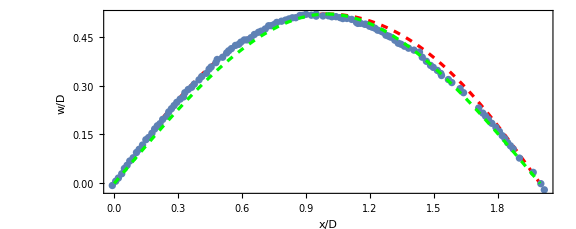
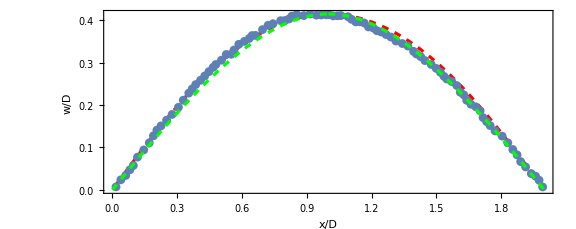
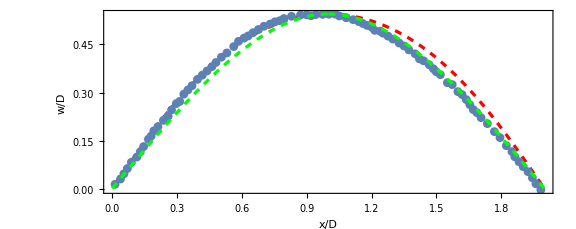
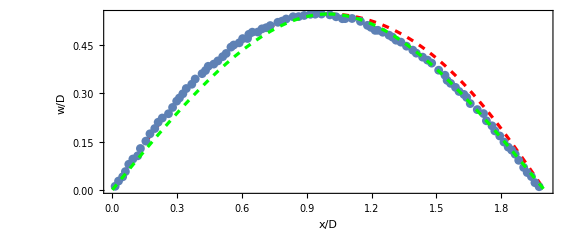
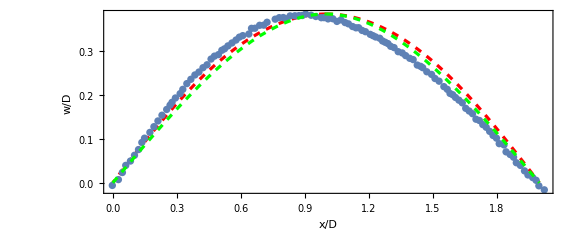
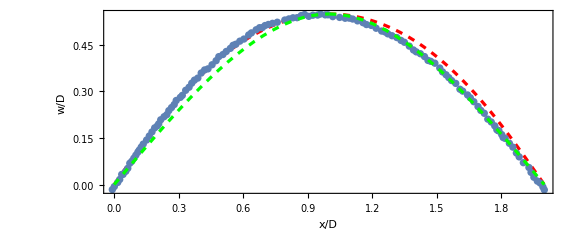
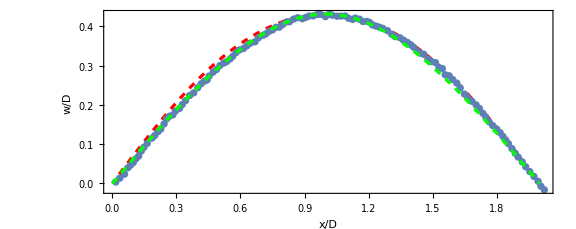
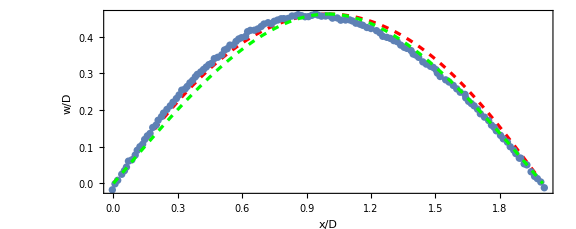
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
fn="EA_"<>ToString[#]&/@EAinx
CompareEA[fn[[#]]]&/@Range[Length@fn]
```

Compare with experimental shape of TA

```mathematica
Get["TAinx"]
```

{1,3,4,6,8,10,11,16,21,23,24,25,26,27,31,34,35,37,40,42,43,44,46,47}

```mathematica
CompareTA[fn_]:=Module[{fname = fn,nn},
SetDirectory[NotebookDirectory[]];
Get[fname];
zw=Partition[Riffle[z,w],2];
pe=ListPlot[zw/DD];
(*nn=If[(F DD^2)/EI>1.6679455178630311,2,3];*)
nn=If[(F DD^2)/EI>1.9161518201003527,{1},{1,3}];
(*nn=1;*)
klist = {gd[dflec/DD],gk[DD kappa],gp[(F DD^2)/EI]};
textlist= {"Same deflection: ","Same curvature : ","Same load      : "};
Colorlist = {Red,Yellow,Purple};
Print["Test ID: ", fn];
Print["{F,δ,k,θ_0,M,κ} : ",Blue,{(F DD^2)/EI,dflec/DD,k,Theta,(F DD)/(2 EI)(DD+dflec*Tan[Theta]),DD kappa}];
pt=Module[{k=klist[[#]]},
solf=NDSolve[{f''[ξ]-k( Cos[f[ξ]]-μ Sin[f[ξ]])==0,f[1]==0,f'[1]==0},f,{ξ,0,1}];
DL=NIntegrate[Cos[(f[ξ]-f[0])/.solf[[1]]],{ξ,0,1}];
δL=NIntegrate[Sin[(f[ξ]-f[0])/.solf[[1]]],{ξ,0,1}];
solx = NDSolve[{x'[s]==-Cos[f[s]-f[0]/.solf[[1]]],x[1]==0},x[s],{s,0,1}];
soly = NDSolve[{y'[s]==Sin[f[s]-f[0]/.solf[[1]]],y[1]==0},y[s],{s,0,1}];
Print[textlist[[#]],Colorlist[[#]],{2k*DL^2 Cos[f[0]/.solf[[1]]],-δL/DL,k,f[0]/.solf[[1]],k(δL/DL Sin[f[0]/.solf[[1]]]+Cos[f[0]/.solf[[1]]]),-D[f[ξ]/.solf[[1]],ξ]/.ξ->0}];
ParametricPlot[{{x[s]/DL/.solx[[1]],y[s]/DL/.soly[[1]]},{2-x[s]/DL/.solx[[1]],y[s]/DL/.soly[[1]]}},{s,0,1},
PlotStyle->Directive[Colorlist[[#]],Thickness[0.004],Dashed],
(*PlotLegends->Placed[{k},{0.5,0.5}],*)
ImageSize->Large,GridLines->None,Ticks->Automatic,AxesStyle->Directive[Black,FontFamily->"Times",16],Frame->True,FrameStyle->Directive[FontFamily->"Times",12],FrameLabel->{Style["x/D",Black,FontFamily->"Times",16],Style["w/D",Black,FontFamily->"Times",16]}]]&/@nn;
AppendTo[pt,pe];
peb=Plot[y[dflec/DD,x],{x,0,2},PlotStyle->Directive[Green,Thickness[0.004],Dashed]];
Show[Append[pt,peb],PlotRange->All]]
```

```mathematica
Isp={1.9161518201003527,0.508754730010644,1.7,0.7291291044265703,0.6915805820664326,1.2088119094315215}
```

{1.91615,0.508755,1.7,0.729129,0.691581,1.20881}

δPCurve = {(F D^2)/(E I),-δ/D,(P L^2)/(E I)=k,-θ_0,-(M D)/(E I),D κ}
δPCurve = {F,δ,k,θ_0,M, κ}

{1.54905,0.249115,0.793491,0.41642,0.859862,0.583019}

{True,True,True,True,False,True}

Test ID: TA_1

{F,δ,k,θ_0,M,κ} : RGBColor[0, 0, 1]{1.54905,0.249115,k,0.41642,0.859862,0.583019}

Same deflection: RGBColor[1, 0, 0]{1.37522,0.249067,0.793491,0.371151,0.667784,0.689266}

Same load      : RGBColor[0.5, 0, 0.5]{1.56071,0.297062,0.955581,0.440413,0.743379,0.803211}

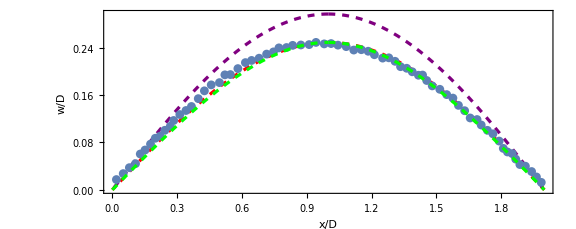

```mathematica
SetDirectory[NotebookDirectory[]];
fn="TA_1";
Get[fn];
ExperData={(F DD^2)/EI,dflec/DD,gd[dflec/DD],Theta,(F DD)/(2 EI)(DD+dflec*Tan[Theta]),DD kappa}
Isp[[#]]>ExperData[[#]]&/@Range[Length@Isp]
CompareTA[fn]
```

δPCurve = {(F D^2)/(E I),-δ/D,(P L^2)/(E I)=k,-θ_0,-(M D)/(E I),D κ}
δPCurve = {F,δ,k,θ_0,M, κ}

{3,5,6,8,9,11,12,13,14,16,17,18,19,21,22,23,26,27,29,30,31,33,34,35,36,37,38,39,40,41,42,43,44}

```mathematica
fn="TA_"<>ToString[#]&/@TAinx;
FexpAll=Table[Fexp[fn[[n]]],{n,1,Length@TAinx}];
ϵexpAll=Table[ϵexp[fn[[n]]],{n,1,Length@TAinx}];
κAll=Table[KappaElastica[fn[[n]]],{n,1,Length@TAinx}]
```

{1283.42,904.66,1490.1,1383.42,643.811,742.376,1318.63,1724.21,1332.39,1032.82,584.942,1541.5,1190.19,1681.65,948.003,1078.39,1326.87,1184.58,1659.75,1438.29,1451.51,1534.48,1228.62,955.45}

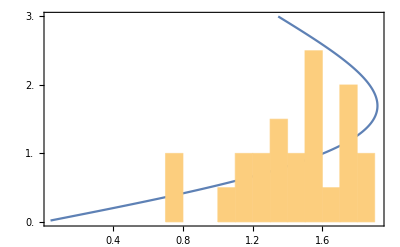

```mathematica
Module[{fgraph,ggraph,frange,grange,fticks,gticks},
{fgraph,ggraph}={ListPlot[δPCurve[[;;,{1,3}]],Joined->True],Histogram[FexpAll,10]};
frange=(PlotRange/.AbsoluteOptions[fgraph,PlotRange])[[2]];
grange={0,6};
fticks=N@FindDivisions[frange,6];
gticks=Quiet@Transpose@{fticks,ToString[NumberForm[#,2],StandardForm]&/@Rescale[fticks,frange,grange]};
Show[fgraph,ggraph/.Graphics[graph_,s___]:>Graphics[GeometricTransformation[graph,RescalingTransform[{{0,1},grange},{{0,1},frange}]],s],Axes->False,Frame->True,FrameStyle->{ColorData[1]/@{1,2},{Automatic,Automatic}},FrameTicks->{{fticks,gticks},{Automatic,Automatic}},
PlotRange->All]
]
```

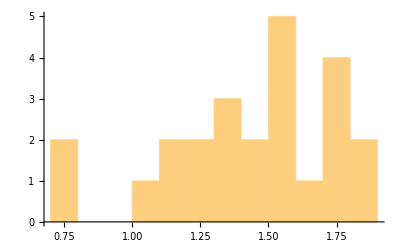

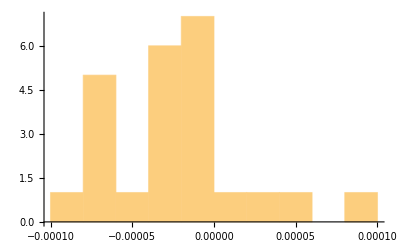

```mathematica
Histogram[FexpAll,10]
Histogram[ϵexpAll,10]
```

{TA_1,TA_3,TA_4,TA_6,TA_8,TA_10,TA_11,TA_16,TA_21,TA_23,TA_24,TA_25,TA_26,TA_27,TA_31,TA_34,TA_35,TA_37,TA_40,TA_42,TA_43,TA_44,TA_46,TA_47}

Test ID: TA_1

{F,δ,k,θ_0,M,κ} : RGBColor[0, 0, 1]{1.54905,0.249115,k,0.41642,0.859862,0.583019}

Same deflection: RGBColor[1, 0, 0]{1.37522,0.249067,0.793491,0.371151,0.667784,0.689266}

Same load      : RGBColor[0.5, 0, 0.5]{1.56071,0.297062,0.955581,0.440413,0.743379,0.803211}

Test ID: TA_3

{F,δ,k,θ_0,M,κ} : RGBColor[0, 0, 1]{1.10685,0.177798,k,0.30164,0.584041,0.429759}

Same deflection: RGBColor[1, 0, 0]{1.03682,0.177839,0.557928,0.266457,0.512112,0.507149}

Same load      : RGBColor[0.5, 0, 0.5]{1.10009,0.190152,0.5982,0.284692,0.542174,0.539664}

Test ID: TA_4

{F,δ,k,θ_0,M,κ} : RGBColor[0, 0, 1]{1.66516,0.289165,k,0.48072,0.958137,0.590781}

Same deflection: RGBColor[1, 0, 0]{1.53249,0.289089,0.928475,0.428989,0.732697,0.784803}

Same load      : RGBColor[0.5, 0, 0.5]{1.66011,0.328025,1.0615,0.48444,0.7772,0.872656}

Test ID: TA_6

{F,δ,k,θ_0,M,κ} : RGBColor[0, 0, 1]{1.73551,0.269897,k,0.40008,0.966796,0.592545}

Same deflection: RGBColor[1, 0, 0]{1.46002,0.269831,0.863299,0.401259,0.703743,0.739477}

Same load      : RGBColor[0.5, 0, 0.5]{1.72364,0.351159,1.14131,0.516967,0.794081,0.92237}

Test ID: TA_8

{F,δ,k,θ_0,M,κ} : RGBColor[0, 0, 1]{0.729864,0.127379,k,0.22251,0.37545,0.302777}

Same deflection: RGBColor[1, 0, 0]{0.76114,0.127468,0.395245,0.191404,0.378443,0.370075}

Same load      : RGBColor[0.5, 0, 0.5]{0.729951,0.122019,0.377854,0.183249,0.363126,0.354883}

Test ID: TA_10

{F,δ,k,θ_0,M,κ} : RGBColor[0, 0, 1]{1.0611,0.145913,k,0.27406,0.552316,0.373657}

Same deflection: RGBColor[1, 0, 0]{0.865333,0.145989,0.454666,0.219075,0.429374,0.4212}

Same load      : RGBColor[0.5, 0, 0.5]{1.06085,0.182475,0.573067,0.273328,0.523566,0.519438}

Test ID: TA_11

{F,δ,k,θ_0,M,κ} : RGBColor[0, 0, 1]{1.55443,0.250369,k,0.45639,0.872751,0.611632}

Same deflection: RGBColor[1, 0, 0]{1.38053,0.25032,0.797689,0.372973,0.670087,0.692334}

Same load      : RGBColor[0.5, 0, 0.5]{1.56564,0.298486,0.96043,0.44245,0.745204,0.806476}

Test ID: TA_16

{F,δ,k,θ_0,M,κ} : RGBColor[0, 0, 1]{1.82524,0.335912,k,0.60786,1.1259,0.829077}

Same deflection: RGBColor[1, 0, 0]{1.6826,0.335839,1.08839,0.495463,0.783728,0.889658}

Same load      : RGBColor[0.5, 0, 0.5]{1.82482,0.398537,1.30651,0.58253,0.804577,1.0182}

Test ID: TA_21

{F,δ,k,θ_0,M,κ} : RGBColor[0, 0, 1]{1.3658,0.259055,k,0.43255,0.764582,0.638113}

Same deflection: RGBColor[1, 0, 0]{1.41662,0.258998,0.826816,0.385576,0.685574,0.71345}

Same load      : RGBColor[0.5, 0, 0.5]{1.36543,0.24677,0.785799,0.367807,0.663518,0.683627}

Test ID: TA_23

{F,δ,k,θ_0,M,κ} : RGBColor[0, 0, 1]{1.20842,0.203481,k,0.30544,0.642974,0.467816}

Same deflection: RGBColor[1, 0, 0]{1.16653,0.203488,0.642037,0.304384,0.573368,0.574412}

Same load      : RGBColor[0.5, 0, 0.5]{1.19365,0.209071,0.660453,0.312607,0.585979,0.588809}

Test ID: TA_24

{F,δ,k,θ_0,M,κ} : RGBColor[0, 0, 1]{0.771104,0.115517,k,0.1659,0.393009,0.255253}

Same deflection: RGBColor[1, 0, 0]{0.692981,0.115608,0.357448,0.173649,0.344932,0.336926}

Same load      : RGBColor[0.5, 0, 0.5]{0.777105,0.130273,0.404214,0.195599,0.386272,0.377869}

Test ID: TA_25

{F,δ,k,θ_0,M,κ} : RGBColor[0, 0, 1]{1.74589,0.29866,k,0.51553,1.02068,0.637737}

Same deflection: RGBColor[1, 0, 0]{1.56597,0.298581,0.960753,0.442586,0.745325,0.806694}

Same load      : RGBColor[0.5, 0, 0.5]{1.73407,0.355318,1.15572,0.52278,0.796321,0.931107}

Test ID: TA_26

{F,δ,k,θ_0,M,κ} : RGBColor[0, 0, 1]{1.38805,0.231981,k,0.43164,0.768182,0.513657}

Same deflection: RGBColor[1, 0, 0]{1.30036,0.231952,0.736328,0.346182,0.634694,0.646866}

Same load      : RGBColor[0.5, 0, 0.5]{1.39104,0.252819,0.806068,0.376606,0.67463,0.698439}

Test ID: TA_27

{F,δ,k,θ_0,M,κ} : RGBColor[0, 0, 1]{1.56297,0.32585,k,0.67852,0.986785,0.84033}

Same deflection: RGBColor[1, 0, 0]{1.65344,0.325773,1.05376,0.481256,0.775164,0.867716}

Same load      : RGBColor[0.5, 0, 0.5]{1.57336,0.300738,0.968102,0.445668,0.748039,0.811626}

Test ID: TA_31

{F,δ,k,θ_0,M,κ} : RGBColor[0, 0, 1]{1.14474,0.186298,k,0.25621,0.600303,0.460256}

Same deflection: RGBColor[1, 0, 0]{1.08064,0.186328,0.585672,0.279034,0.532963,0.529609}

Same load      : RGBColor[0.5, 0, 0.5]{1.13358,0.196817,0.620082,0.294541,0.557949,0.557093}

Test ID: TA_34

{F,δ,k,θ_0,M,κ} : RGBColor[0, 0, 1]{1.35754,0.210113,k,0.33517,0.728445,0.5096}

Same deflection: RGBColor[1, 0, 0]{1.19866,0.210111,0.663888,0.314138,0.588297,0.591481}

Same load      : RGBColor[0.5, 0, 0.5]{1.35591,0.244554,0.778383,0.364579,0.65935,0.678172}

Test ID: TA_35

{F,δ,k,θ_0,M,κ} : RGBColor[0, 0, 1]{1.55233,0.258446,k,0.36025,0.851727,0.617313}

Same deflection: RGBColor[1, 0, 0]{1.41413,0.25839,0.824773,0.384695,0.684516,0.711979}

Same load      : RGBColor[0.5, 0, 0.5]{1.56372,0.29793,0.958537,0.441655,0.744495,0.805203}

Test ID: TA_37

{F,δ,k,θ_0,M,κ} : RGBColor[0, 0, 1]{1.44606,0.231552,k,0.37841,0.789591,0.573366}

Same deflection: RGBColor[1, 0, 0]{1.29843,0.231523,0.734901,0.345555,0.633827,0.645793}

Same load      : RGBColor[0.5, 0, 0.5]{1.45645,0.268921,0.860228,0.399944,0.702268,0.737305}

Test ID: TA_40

{F,δ,k,θ_0,M,κ} : RGBColor[0, 0, 1]{1.70321,0.320246,k,0.55182,1.0195,0.78304}

Same deflection: RGBColor[1, 0, 0]{1.63644,0.320168,1.03452,0.47332,0.769804,0.855344}

Same load      : RGBColor[0.5, 0, 0.5]{1.69317,0.339642,1.10151,0.500815,0.786604,0.897857}

Test ID: TA_42

{F,δ,k,θ_0,M,κ} : RGBColor[0, 0, 1]{1.75665,0.275343,k,0.39017,0.977782,0.606506}

Same deflection: RGBColor[1, 0, 0]{1.48112,0.275274,0.881677,0.409116,0.712368,0.75241}

Same load      : RGBColor[0.5, 0, 0.5]{1.74526,0.359917,1.17167,0.529195,0.798509,0.940696}

Test ID: TA_43

{F,δ,k,θ_0,M,κ} : RGBColor[0, 0, 1]{1.567,0.282666,k,0.44948,0.89034,0.605276}

Same deflection: RGBColor[1, 0, 0]{1.50873,0.282593,0.906444,0.419657,0.723421,0.76965}

Same load      : RGBColor[0.5, 0, 0.5]{1.57697,0.301798,0.971714,0.447182,0.749351,0.814044}

Test ID: TA_44

{F,δ,k,θ_0,M,κ} : RGBColor[0, 0, 1]{1.80683,0.295154,k,0.45233,1.03299,0.687249}

Same deflection: RGBColor[1, 0, 0]{1.55379,0.295077,0.948825,0.437572,0.740792,0.798647}

Same load      : RGBColor[0.5, 0, 0.5]{1.80238,0.386293,1.26359,0.565726,0.805078,0.994217}

Test ID: TA_46

{F,δ,k,θ_0,M,κ} : RGBColor[0, 0, 1]{1.48762,0.239097,k,0.30428,0.799659,0.558748}

Same deflection: RGBColor[1, 0, 0]{1.33198,0.23906,0.760026,0.356568,0.648799,0.664583}

Same load      : RGBColor[0.5, 0, 0.5]{1.50075,0.280455,0.899204,0.416581,0.720258,0.764633}

Test ID: TA_47

{F,δ,k,θ_0,M,κ} : RGBColor[0, 0, 1]{1.20992,0.187124,k,0.32162,0.642677,0.432183}

Same deflection: RGBColor[1, 0, 0]{1.08485,0.187153,0.588374,0.280255,0.53496,0.531782}

Same load      : RGBColor[0.5, 0, 0.5]{1.19514,0.20938,0.661472,0.313061,0.586668,0.589602}

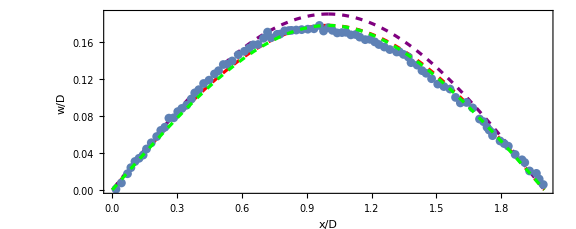
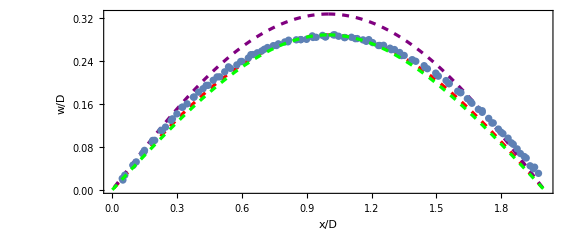
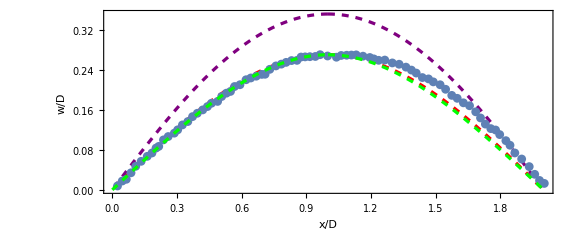
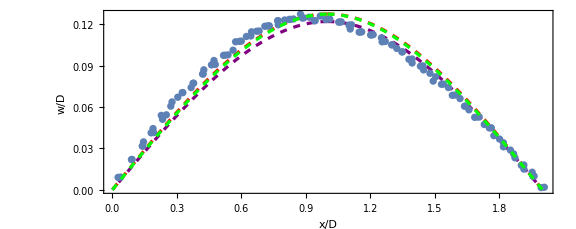
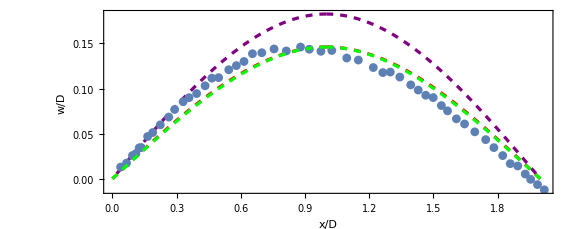
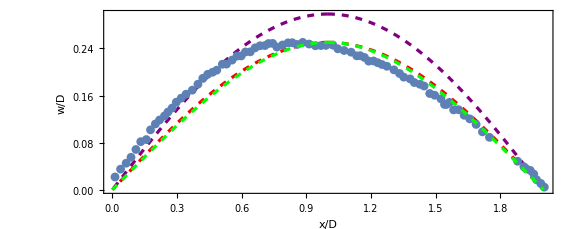
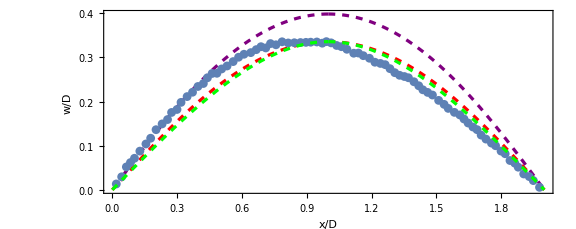
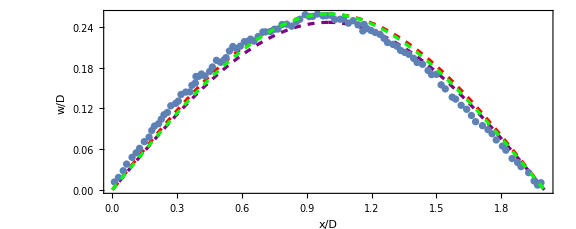
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
fn="TA_"<>ToString[#]&/@TAinx
FexpAll=Table[Fexp[fn[[n]]],{n,1,Length@TAinx}];
ϵexpAll=Table[ϵexp[fn[[n]]],{n,1,Length@TAinx}];
CompareTA[fn[[#]]]&/@Range[Length@fn]
```